#### Introduction

Suppose a cutset of size S splits K(n, r) into c components.
u is an upper bound of the number of crossing edges e(S,K(n,r)\S).

```mathematica
u[n_,r_,c_,S_]:=With[{d=Binomial[n-r,r]},Min[d*S,Floor[((d+Binomial[n-r-1,r-1])S(Binomial[n,r]-S))/Binomial[n,r]]]]
```

a is a lower bound on how many of the c components are singletons.

```mathematica
a[n_,r_,c_,S_]:=With[{d=Binomial[n-r,r]},Ceiling[(-2 c+2 c d-u[n,r,c,S])/(-2+d)]]
```

f is a lower bound on the number of edges from a single component to S.
To minimize toughness, no component may be a tree except possibly a K_2 or K_1.

```mathematica
f[10,4,1]=15;
f[10,4,2]=28;
f[10,4,4]=52;
f[10,4,5]=63;
f[10,4,6]=72;
f[10,4,7]=72;
f[10,4,8]=72;
f[10,4,t_/;t≤95]:=f[10,4,t]=Ceiling[(9t(210-t))/210];
f[10,4,t_/;t≥96]:=f[10,4,t]=470
```

```mathematica
f[9,4,1]=5;
f[9,4,2]=8;
f[9,4,6]=18;
f[9,4,7]=21;
f[9,4,8]=22;
f[9,4,9]=25;
f[9,4,t_]:=f[9,4,t]=Ceiling[(2t(126-t))/126];
```

```mathematica
f[7,3,1]=4;
f[7,3,2]=6;
f[7,3,6]=12;
f[7,3,7]=14;
f[7,3,t_]:=f[7,3,t]=Ceiling[(2t(35-t))/35];
```

p is a list of partitions of the remaining vertices into the c-a components which do not exceed the upper bound.

```mathematica
KneserGirth[n_,r_]:=Min[If[n==2r+1,6,4],2Ceiling[r/(n-2r)]+1]
```

```mathematica
l[n_,r_,part_]:=Total[f[n,r,#]&/@part]
```

```mathematica
p[n_,r_,c_,S_,lim_]:=With[{
parts=IntegerPartitions[Binomial[n,r]-S-a[n,r,c,S],{c-a[n,r,c,S]},Join[{1,2},Range[KneserGirth[n,r],Binomial[n,r]-S-c+1]]]
},Select[parts,l[n,r,#]≤lim&]];
p[n_,r_,c_,S_]:=p[n,r,c,S]=p[n,r,c,S,u[n,r,c,S]-Binomial[n-r,r]a[n,r,c,S]]
```

#### Testing

From spectral bounds, we only need to test 48≤c≤75 for K(10, 4).
For 48≤c≤70, we can search from S=⌈3/2 c⌉-1 downwards until there exist no more partitions.

```mathematica
Table[p[10,4,c,#]&/@TakeWhile[Range[Ceiling[3/2 c]-1,c+1,-1],p[10,4,c,#]≠{}&],{c,48,70}]
```

{{},{},{},{},{},{},{},{},{},{{{69,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{70,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{67,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{64,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{62,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{59,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{57,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{54,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{52,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{49,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{47,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{44,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{42,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{39,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},{{{37,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}}

For 71≤c≤75, we need to test each S.

```mathematica
Table[p[10,4,c,#]&/@Range[Ceiling[3/2 c]-1,c+1,-1],{c,71,75}]
```

{{{{34,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{{32,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{{29,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{{27,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{{24,1,1,1,1,1,1,1,1,1,1,1,1}},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}}

From spectral bounds, we only need to test 5≤c≤53 for K(9, 4).
All partitions for each c and S.

```mathematica
Table[Table[p[9,4,c,S],{S,c+1,Ceiling[5/4 c]-1}],{c,5,53}]
```

{{{}},{{}},{{}},{{}},42,{{},{},{},{},{},{},{{18,1,1,1,1,1,1,1}},{{17,1,1,1,1,1,1,1,1},{16,2,1,1,1,1,1,1,1}},{{16,1,1,1,1,1,1,1,1},{15,2,1,1,1,1,1,1,1},{14,2,2,1,1,1,1,1,1}},{{15,1,1,1,1,1,1,1,1},{14,2,1,1,1,1,1,1,1},{13,2,2,1,1,1,1,1,1},{12,2,2,2,1,1,1,1,1},{11,2,2,2,2,1,1,1,1},{10,6,1,1,1,1,1,1,1}},{{14,1,1,1,1,1,1,1,1},{13,2,1,1,1,1,1,1,1},{12,2,2,1,1,1,1,1,1},{11,2,2,2,1,1,1,1,1},{10,2,2,2,2,1,1,1,1}},{{13,1,1,1,1,1,1,1,1},{12,2,1,1,1,1,1,1,1},{11,2,2,1,1,1,1,1,1},{10,2,2,2,1,1,1,1,1}}},{{},{},{},{},{},{},{},{{15,1,1,1,1,1,1}},{{14,1,1,1,1,1,1},{13,2,1,1,1,1,1},{12,2,2,1,1,1,1}},{{13,1,1,1,1,1,1},{12,2,1,1,1,1,1},{11,2,2,1,1,1,1},{10,2,2,2,1,1,1}},{{12,1,1,1,1,1,1},{11,2,1,1,1,1,1},{10,2,2,1,1,1,1}},{{11,1,1,1,1,1,1},{10,2,1,1,1,1,1}}},{{},{},{},{},{},{},{},{},{{12,1,1,1,1,1}},{{11,1,1,1,1,1},{10,2,1,1,1,1}},{{10,1,1,1,1,1}},{},{{8,1,1,1,1}}}}
 |  |  |  |

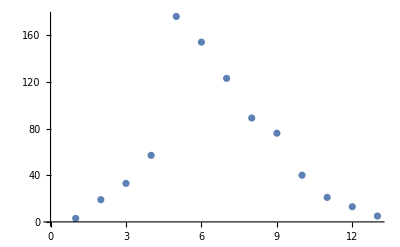

```mathematica
ListPlot[{3,19,33,57,176,154,123,89,76,40,21,13,5}]
```

```mathematica
Table[Table[u[9,4,c,S]-5a[9,4,c,S]-l[9,4,#]&/@p[9,4,c,S],{S,c+1,Ceiling[5/4 c]-1}],{c,5,53}]
```

{{{}},{{}},{{}},{{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{},{}},{{},{},{},{}},{{},{},{},{}},{{},{},{},{}},{{},{},{},{},{}},{{},{},{},{},{}},{{},{},{},{},{}},{{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{},{}},{{},{},{},{},{},{},{}},{{},{},{},{},{},{},{}},{{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{},{4,2,0}},{{},{},{},{},{},{},{},{},{0},{6,4,2,0,2,1,0,1,1,0,1,0,1,0,0,0,0,0}},{{},{},{},{},{},{},{},{},{2,0},{8,6,4,2,0,0,4,4,3,4,2,1,3,2,0,4,2,1,3,2,0,4,2,1,0,3,3,2,2,1,0}},{{},{},{},{},{},{},{},{},{4,2,0,1,0,0,0,0,0,0},{10,8,6,4,2,3,1,1,1,1,0,0,7,6,5,7,5,4,6,5,3,2,7,5,4,2,1,6,5,3,2,0,1,4,2,1,1,0,0,0,1,0,0,0,0,6,5}},{{},{},{},{},{},{},{},{0},{6,4,2,0,3,3,2,3,1,0,3,2,0,3,1,0,2,0,3},{12,10,8,7,5,5,3,4,4,2,4,2,2,0,2,2,0,0,10,1,1,9,8,10,8,7,9,8,6,5,10,8,7,5,4,6,5,3,4,2,4,4,2,3,3,1,2,2,0,3,1,1,2,2,0,0},{18,16,15,13,11,12,10,10,10,8,10,8,8,6,9,9,7,7,5,16,7,7,5,5,3,16,15,6,6,4,6,4,2,16,14,13,4,4,4,2,4,2,0,16,15,13,12,3,5,3,3,3,1,3,1,14,13,11,10,3,1,3,3,1,1,1,1,12,10,11,9,2,2,0,4,2,2,0,0,0,0,10,8,9,9,7,2,0,0,2,0,0,0,10,8,8,6,1,1,1}},{{},{},{},{},{},{},{},{2,0,0,0,0},{8,6,5,3,1,2,0,0,0,0,6,6,5,6,4,3,6,5,3,2,4,3,1,0,2,0,1,0,0},{14,13,11,9,8,8,6,6,6,4,7,5,5,3,5,5,3,3,1,13,4,4,2,2,0,12,11,2,2,0,2,0,13,11,10,1,1,1,1,12,11,9,8,1,10,8,7,0,0,0,6,7,5,0,6,6,4},{16,14,12,11,9,9,7,8,8,6,8,6,6,4,7,7,5,5,3,14,5,5,3,3,1,14,13,4,4,2,4,2,0,14,12,11,2,2,2,0,2,0,13,11,10,1,3,1,1,1,1,9,8,1,1,1,9,7,0,0,2,0,0}},{{},{},{},{},{},{},{},{4,3,1,3,2,1,3,1,0,2,1,0},{11,9,7,6,4,4,2,3,3,1,3,1,1,2,2,0,0,9,0,0,9,8,9,7,6,8,6,5,4,3,4,2},{12,10,9,7,5,6,4,4,4,2,5,3,3,1,3,3,1,1,11,2,2,0,0,10,9,0,0,0,11,9,8,7,6,5},{14,13,11,9,8,8,6,7,7,5,7,5,5,3,6,6,4,4,2,13,4,4,2,2,0,13,12,3,3,1,3,1,11,10,1,1,1,1,9,0,2,0,0,0,0}},{{},{},{},{},{},{},{1},{7,5,4,2,0,1,0,6,5,4,6,4,3,2,1,0},{8,7,5,3,2,2,0,1,1,1,0,0,7,7,6,5,4,3},{11,9,7,6,4,5,3,3,3,1,4,2,2,0,2,2,0,0,10,1,1,9,8,7},{13,11,10,8,7,7,5,6,6,4,6,4,4,2,5,5,3,3,1,12,3,3,1,1,11,2,2,0,2,0}},{{},{},{},{},{},{},{3,2,0,2,2,1,0},{5,3,1,0,4,3,2,1},{7,5,4,2,1,1,0,0,0,6,5},{9,8,6,5,3,4,2,2,2,0,3,1,1,1,1,9,0,0},{11,9,8,6,5,5,3,4,4,2,4,2,2,0,3,3,1,1},{13,12,10,9,7,8,6,6,6,4,7,5,5,3}},{{},{},{},{},{},{0},{1,0},{3,2,0,3},{6,4,3,1,0,0},{7,6,4,3,1,2,0,0,0,1},{10,8,7,5,4,4,2,3,3,1},{11,10,8,7,5,6,4}},{{},{},{},{},{},{},{0},{2,1},{4,2,1},{6,5,3,2,0,1},{8,6,5,3,2},{9,8,6,5}},{{},{},{},{},{},{},{},{0},{3,1,0},{4,3,1,0},{6,4,3},{7,6}},{{},{},{},{},{},{},{},{},{1},{2,1},{4},{},{0}}}

```mathematica
Max@%39
```

```mathematica
18
```

```mathematica
Flatten[Table[Table[{u[9,4,c,S]-5a[9,4,c,S]-l[9,4,#],#,c,S}&/@p[9,4,c,S],{S,c+1,Ceiling[5/4 c]-1}],{c,41,41}],2]
```

{{4,{35,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},41,51},{2,{34,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1},41,51},{0,{33,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1},41,51}}

```mathematica
Sort@Flatten[Table[Table[{u[9,4,c,S]-5a[9,4,c,S]-l[9,4,#],#,c,S}&/@p[9,4,c,S],{S,c+1,Ceiling[5/4 c]-1}],{c,5,53}],2]
```

{{0,{8,1,1,1,1},53,66},{0,{10,2,2,2,1,1,1},52,62},{0,{12,2,2,1,1,1,1},52,61},{0,{15,1,1,1,1,1,1},52,60},{0,{18,1,1,1,1,1,1,1},51,58},{0,{11,2,2,2,2,1,1,1,1},51,61},{0,{11,6,2,1,1,1,1,1,1,1},50,60},{0,{11,7,1,1,1,1,1,1,1,1},50,60},{0,{11,10,1,1,1,1,1,1,1,1},50,57},{0,{12,2,2,2,2,2,1,1,1,1},50,60},{0,{13,6,1,1,1,1,1,1,1,1},50,59},787,{14,{15,11,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56},{15,{14,12,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56},{15,{16,10,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56},{15,{24,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56},{16,{24,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},46,57},{16,{14,13,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56},{16,{15,12,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56},{16,{16,11,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56},{16,{17,10,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56},{16,{25,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56},{18,{26,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},45,56}}
 |  |  |  |

```mathematica
SortBy[%57,Count[#⟦2⟧,2]&]//Reverse
```

{{0,{15,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1},45,56},{2,{16,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1},45,56},{0,{14,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1},46,57},{3,{17,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1},45,56},{1,{15,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1},46,57},{0,{16,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1},46,56},{0,{13,2,2,2,2,2,2,2,2,2,1,1,1,1,1},47,58},{5,{18,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1},45,56},{3,{16,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1},46,57},{2,{14,2,2,2,2,2,2,2,2,1,1,1,1,1,1},47,58},{1,{17,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1},46,56},787,{0,{14,14,1,1,1,1,1,1,1,1,1,1,1},46,54},{0,{14,9,1,1,1,1,1,1,1,1,1,1,1},48,57},{0,{14,7,1,1,1,1,1,1,1,1,1,1},49,58},{0,{13,8,1,1,1,1,1,1,1,1,1,1},49,58},{0,{21,1,1,1,1,1,1,1,1,1},50,56},{0,{13,6,1,1,1,1,1,1,1,1},50,59},{0,{11,10,1,1,1,1,1,1,1,1},50,57},{0,{11,7,1,1,1,1,1,1,1,1},50,60},{0,{18,1,1,1,1,1,1,1},51,58},{0,{15,1,1,1,1,1,1},52,60},{0,{8,1,1,1,1},53,66}}
 |  |  |  |

K(7,3)

```mathematica
Table[Table[p[7,3,c,S],{S,c+1,Ceiling[(7/3-1)c]-1}],{c,5,13}]
```

{{{}},{{}},{{},{}},{{},{}},{{},{}},{{},{},{}},{{},{},{{11,1,1,1,1,1}}},{{},{},{{9,1,1,1,1,1},{8,2,1,1,1,1}}},{{},{},{},{{6,1,1,1}}}}

#### LaTeX

```mathematica
Import["https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"]
```

```mathematica
Cells[]⟦3⟧//NotebookRead
```

Cell[BoxData[{RowBox[{RowBox[{RowBox[{a,[,RowBox[{n_,,,r_,,,c_,,,S_}],]}],:=,RowBox[{With,[,RowBox[{RowBox[{{,RowBox[{d,=,RowBox[{Binomial,[,RowBox[{RowBox[{n,-,r}],,,r}],]}]}],}}],,,RowBox[{Ceiling,[,RowBox[{RowBox[{FractionBox[RowBox[{RowBox[{2,d}],-,2}],RowBox[{d,-,2}]],c}],-,RowBox[{FractionBox[d,RowBox[{d,-,2}]],S}]}],]}]}],]}]}],;}],
,RowBox[{RowBox[{a,[,RowBox[{n_,,,r_,,,c_}],]}],:=,RowBox[{a,[,RowBox[{n,,,r,,,c,,,RowBox[{RowBox[{Ceiling,[,RowBox[{RowBox[{(,RowBox[{FractionBox[n,r],-,1}],)}],c}],]}],-,1}]}],]}]}]}],Input,InitializationGroup→True,CellChangeTimes→{{3.79916×10^9,3.79916×10^9},{3.79916×10^9,3.79916×10^9},{3.79916×10^9,3.79916×10^9},{3.79916×10^9,3.79916×10^9},{3.79925×10^9,3.79925×10^9},{3.79925×10^9,3.79925×10^9},{3.79925×10^9,3.79925×10^9},{3.79925×10^9,3.79925×10^9},{3.79933×10^9,3.79933×10^9},{3.79934×10^9,3.79934×10^9}},CellLabel→In[1]:=]

```mathematica
CellToTeX[NotebookRead[Cells[]⟦13⟧]]
```

\begin{mmaCell}[moredefined={l, f, p},morepattern={n_, r_, c_, S_, n, r, c, S, \#}]{Input}
  l[n_,r_,c_,S_]:=l[n,r,c,S]=Total[f[n,r,#]&/@First[p[n,r,c,S,1]]];
  l[n_,r_,c_]:=l[n,r,c]=l[n,r,c,Ceiling[(\mmaFrac{n}{r}-1)c]-1]
\end{mmaCell}